## 2-adic Mandelbrot Set Calculations

This notebook contains Mathematica functions that implement the algorithms given in Algorithms for Classifying Points in a 2-adic Mandelbrot Set by Bate, Craft, and Yuly. Code is contained in collapsible sections.

### Helper Functions

These helper functions are used by other functions in the notebook.

maxIndepPower2 is a function that has input:

	next = an algebraic expression given in terms of variables (given in indetVars)
	m = maximum (to be described shortly)
	indetVars = list of variables in next.

This function finds the highest power j such that next ≡ c (mod 2^j). The function then return { c, j }.

This function assumes Length[indetVars] equals 2 or 3.

```mathematica
maxIndepPower2[next_,m_,indetVars_]:=Module[{nonZeroConstLst,modNext,k,d,curMax,foundTrueMax,g,testModNext,i1,i2,i3},
	(* This list is used shortly. *)
	nonZeroConstLst=ConstantArray[1,Length[indetVars]];

	(* We find k for which next(mod 2^(m-k)) is constant (i.e. independent of indetVars). *)
	For[k=0,k≤m-1,k++,
		modNext=PolynomialMod[next,2^(m-k)];

		(* We see if modNext still has variables remaining. This next step requires some explanation. If modNext≠0 then 
				CoefficientList[modNext,indetVars]={..{modNext}..} where the number of {}'s is equal to Length[indetVars].
		Then 
				d = Dimensions[CoefficientList[modNext,indetVars]] = nonZeroConstLst. 
		If instead modNext=0 then 
				CoefficientList[modNext,indetVars]={} and so d = Dimensions[CoefficientList[modNext,indetVars]] = {0}. 
		If modNext is non-constant then, to put it succinctly, we do not have d equal nonZeroConstLst nor {0}. *)
		d=Dimensions[CoefficientList[modNext,indetVars]];
		If[d==nonZeroConstLst||d=={0},Break[];];
];

	(* m-k may not be the true j we are looking for. That's because Mathematica's PolomialMod function cannot recognize
	certain algebraic expressions as reducing to a constant. Unfortunately, we need to see if there are powers higher 
	than m-k where are constant. *)
	curMax=m-k;
	foundTrueMax = False;
	g=Function[Evaluate@indetVars,next]; (* We make next a function of indetVars. *)

	(* For 2 variables *)
	If[Length[indetVars]==2,
		While[!foundTrueMax,
			testModNext=g[0,0];
			(* We plug in for all possible inputs to see if we have consistency throughout.*)
			For[i1=0,i1<2^(curMax+1)&&!foundTrueMax,i1++,
				For[i2=0,i2<2^(curMax+1)&&!foundTrueMax,i2++,
					If[testModNext≠g[i1,i2],foundTrueMax=True; ];
				];
			];

			(* If we haven't found the true max, then we must test curMax+1. If it turns out curMax+1 is not
			well-defined, then we can look back at modNext to see what testModNext was for curMax. *)
			If[!foundTrueMax,curMax++;modNext=testModNext];
		];

		Return[{modNext,curMax}];
	];

	(* For 3 variables *)
	If[Length[indetVars]==3,
		While[!foundTrueMax,
			testModNext=g[0,0,0];
			(* We plug in for all possible inputs to see if we have consistency throughout.*)
			For[i1=0,i1<2^(curMax+1)&&!foundTrueMax,i1++,
				For[i2=0,i2<2^(curMax+1)&&!foundTrueMax,i2++,
					For[i3=0,i3<2^(curMax+1)&&!foundTrueMax,i3++,
						If[testModNext≠g[i1,i2,i3],foundTrueMax=True; ];
					];
				];
			];

			(* If at this point we haven't found the true max, then we must test curMax+1. If it turns out curMax+1 is not
			well-defined, then we can look back at modNext to see what testModNext was for curMax. *)
			If[!foundTrueMax,curMax++;modNext=testModNext];
		];

		Return[{modNext,curMax}];
	];
];
```

Gives the two-adic valuation for rational numbers:

```mathematica
TwoVal[x_]:=IntegerExponent[Numerator[x],2]-IntegerExponent[Denominator[x],2];
```

Gives the two-adic absolute value for rational numbers:

```mathematica
Abs2[x_]:=2^(-TwoVal[x]);
```

### Implementation of Algorithm 4.7 (orb)

The function orb is an implementation of Algorithm 4.7. The input of orb mirrors the notation used in Algorithm 4.7, but instead of using N to indicate an index upper bound we use M (since N is a reserved keyword in Mathematica). To reiterate, we assume a0 is odd and b0 is even. orb returns output of the form:

	{fType, fnAbs, cn, jn}

where fType categorizes f in the following way:

	fType 
	= 5 if α is in the basin of attraction of zero
	= 4 if |f^n(α)| stabilizes to 1/2
	= 3 if f^n(α) is bounded because both 4 and 5 occur as sub-cases
	= 2 if f^n(α) has modular periodicity (i.e. satisfies (4.8))
	= 0 if inconclusive due to small j or k (i.e. c_(n+1)=0 and j_(n+1)≤2)
	= -1 if inconclusive due to small M
	= -2 if f^n(α) is unbounded.

We also have that

	fAbs gives the sequence |f^n(α)|
	cn gives the sequence c_n
	jn gives the sequence j_n.

```mathematica
orb[a0_,b0_,j_,k_,M_]:=Module[{f,cn,jn,fnAbs,fType,p,q,pn,i,i2,next,cnNext,jnNext,cnNextInd},
	f[x_]:=x(x^2-(3((a0+2^j p)+(b0+2^k q)))/2 x+3(a0+2^j p) (b0+2^k q)); (* f(x) as defined in (4.1) *)

	cn={4a0}; (* This stores Subscript[c, n] *)
	jn={j+2}; (* This stores Subscript[j, n] *)
	fnAbs={};  (* Stores |f^n(α)| *)
	fType = -1;  (* We assume things are inconclusive from the outset. *)

	For[i=1,i≤M,i++,
		If[fType≠-1,Break[];]; (* Kills the loop if orbit already classified. *)
		next=4f[(cn[[i]]+2^jn[[i]] pn)/4];

		(* We find Subscript[c, n+1] and Subscript[j, n+1]; see (4.4), (4,5), or Algorithm 4.7 for details. *)
		{cnNext,jnNext}=maxIndepPower2[next,Min[j,k],{p,q,pn}];

	cn=Append[cn,cnNext];
	jn=Append[jn,jnNext];
	(* The next computation uses the Algorithm 4.7(a) to compute |f^n(α)| along with the fact that
			|Subscript[c, n]|=2^-e ⇔ Subscript[c, n]≡2^e(mod 2^(e+1)) ⇔ |f^n(α)|=2^(2-e), which implies |f^n(α)|=|Subscript[c, n]/4|,
		for Subscript[c, n]≠0. *)
	If[cnNext≠0,fnAbs=Append[fnAbs,Abs2[cnNext/4]]];

	(* We test for Algorithm 4.6(b); this means f^n(α) is unbounded. *)
	If[Mod[cnNext,2]==1&&jnNext>0,fType=-2;Break[];] ;
	(* We test for Algorithm 4.6(c), using Lemma 4.4(a) to determine if α is in basin of zero. *)
	If[Mod[cnNext,16]==0&&jnNext≥4,fType=5;Break[];];
	(* We test for Algorithm 4.6(c), using Lemma 4.4(b) to determine if |f^n(α)| stabilizes to 1/2. *)
	If[Mod[cnNext,16]==8&&jnNext≥4,fType=4;Break[];];
	 (* We test for Algorithm 4.6(c); if here then we know f^n(α) is bounded but can't say anything beyond this. *)
	If[Mod[cnNext,8]==0&&jnNext==3,fType=3;Break[];];  
	
	(* We test if we must terminate the sequence because Subscript[c, n+1]=0 and Subscript[j, n+1]≤2. Inconclusive due to small m. *)
	If[cnNext==0&&jnNext≤2,fType=0;Break[];]; 

	(* We check for modular preperiodicity. *)
	If[ MemberQ[Drop[cn,-1],cnNext], (* Check if the value of Subscript[c, n+1] (cnNext) has already appeared in prior Subscript[c, n]. *)
			(* This finds all indices in {Subscript[c, n]} where the value of Subscript[c, n+1] has already appeared. *)
			cnNextInd=Flatten[Position[Drop[cn,-1],cnNext]];
			(* We loop through these indices checking if we find a corresponding Subscript[j, n] entry that matches the value of Subscript[j, n+1]. *)
			For[i2=1,i2≤Length[cnNextInd],i2++,
				If[jn[[cnNextInd[[i2]]]]==jnNext,fType=2;Break[];];
			];
		];
	];

	Return[{fType,fnAbs,cn,jn}];
];
```

### Slow Approach (slowOrb)

slowOrb takes the following input:

	α an integer,
	β an integer,
	M a positive integer.

slowOrb computes  and |f^n(α)| and |f^n(β)| up to at most n=M using old-fashioned iteration. As its name suggests, it is slow. The function terminates once the conditions specified in Proposition 4.6 are reached. slowOrb returns

	{αType,αAbs, βType, βAbs}.

αType	= 5 if α is in the basin of attraction of zero
	= 4 if |f^n(α)| stabilizes to 1/2
            = -1 if classification inconclusive due to small M.
            = -2 if f is not in ℳ

αAbs gives the sequence|f^n(α)| that were computed.

βType and βAbs are defined similarly.

```mathematica
slowOrb[α_,β_,M_]:=Module[{f,αOrb,αAbs,αType,i,next,nextAbs,βOrb,βAbs,βType},
	f[x_]:=x(x^2-(3(α+β))/2 x+3α β);
	αOrb={α};
	αAbs={};
	αType=-1;

	For[i=1,i≤M,i++,
		next=f[Last[αOrb]];
		αOrb=Append[αOrb,next];
		nextAbs=Abs2[next];
		αAbs=Append[αAbs,nextAbs];
		If[nextAbs≤1/4,αType=5;Break[];];
		If[nextAbs==1/2,αType=4;Break[];];
		If[nextAbs≥4,αType=-2;Break[];];
	];

	βOrb={β};
	βAbs={};
	βType=-1;

	For[i=1,i≤M,i++,
		next=f[Last[βOrb]];
		βOrb=Append[βOrb,next];
		nextAbs=Abs2[next];
		βAbs=Append[βAbs,nextAbs];
		If[nextAbs≤1/2,βType=2;Break[];];
		If[nextAbs≥4,βType=-2;Break[];];
	];

	Return[{αType,αAbs,βType,βAbs}];
];
```

### slowOrb vs orb

We test that orb and slowOrb produce (roughly) the same results. There will be differences from time to time since orb can detect modular periodicity, but otherwise they should be the same. Also, we will also have fType and αTypeSlow disagree at times since orb has more robust classification methods.

```mathematica
slowOrbVsOrbTest[uppBnd_,M_,m_]:=Module[{i,j,α,β,αTypeSlow,αAbsSlow,βTypeSlow,βAbsSlow,fType,fnAbs,cn,jn},

	For[i=0,i≤uppBnd,i++,
		For[j=0,j≤uppBnd,j++,
			α=2i+1;
			β=2j;

			{αTypeSlow,αAbsSlow,βTypeSlow,βAbsSlow}=slowOrb[α,β,M];
			{fType,fnAbs,cn,jn}=orb[α,β,m,m,M];

			If[αAbsSlow≠fnAbs,
				Print["α=",α," ,β=",β];
				Print["{αTypeSlow,αAbsSlow,βTypeSlow,βAbsSlow}=",{αTypeSlow,αAbsSlow,βTypeSlow,βAbsSlow}];
				Print["{fType,fnAbs}=",{fType,fnAbs}];
			];
		];
	];
];
```

```mathematica
slowOrbVsOrbTest[100,10,30]
```

α=161 ,β=142

{αTypeSlow,αAbsSlow,βTypeSlow,βAbsSlow}={-1,{2,2,2,1,2,2,2,1,2,2},2,{1/2}}

{fType,fnAbs}={2,{2,2,2,1,2,2,2,1,2}}

### Figures for Algorithm 4.7 (orbTab & orbTabTeX)

This section contains commands for generating image tables using orb. 

The following two functions are used for constructing Mathematica generated graphics. imgBuild simply makes a 20 by 20 square with the specified color. orbTab creates a colored grid with entries specified according to the designations given in Section 4. The input m for orbTab specifies a common value for j and k in Algorithm 4.7. The input M specifies an index upper bound for when orbTab applies orb. The inputs a0Upp and b0Upp specify the largest possible values for a0 and b0 when applying orbTab.

```mathematica
imgBuild[color_]:=Image[Table[color,{k1,0,20},{k2,0,20}]]

orbTab[m_,M_,a0Upp_,b0Upp_]:=Module[{tab,i,j,row,a0,b0,fType,fnAbs,cn,jn,βType,img},
tab={}; (* This will store our image table data.*)
For[i=0,2i+1<a0Upp,i++,
row={};
For[j=0,2j<b0Upp,j++,
a0=2i+1; (* a0 is always odd *)
b0=2j; (* b0 is always even *)
{fType,fnAbs,cn,jn}=orb[a0,b0,m,m,M]; (* I assume j=k=m. This can be easily adapted if needed. *)

img=imgBuild[White]; (* This will persists if fType == -1 or 0. This represents failure to classify. *)

If[fType==5,img=imgBuild[Cyan]]; (* α in basin of attraction of zero *)
If[fType==4,img=imgBuild[Yellow]]; (* |f^n(α)| stabilizes to 1/2 *)
If[fType==3,img=imgBuild[Green]]; (* f^n(α) is bounded, but nothing else is known *)
If[fType==2,img=imgBuild[Blue]]; (* |f^n(α)| has modular perperiodicity *)
(*If[fType==-1,img=imgBuild[Black]];*)
If[fType==-2,img=imgBuild[Blend[{Red,Orange},.5]]]; (* |f^n(α)| is unbounded *)

row=Append[row,img];
];
tab=Append[tab,row];
];
 Return[ImageAssemble[tab]]; 
];
```

The following code generates nice table image.

```mathematica
ImagePad[orbTab[7,50,29,29],2]
```

-Graphics-

```mathematica
ImagePad[orbTab[15,50,110,110],2]
```

-Graphics-

The function orbTabTeX is used for generating tikz code for Figure 1. It’s essentially the same as orbTab but makes reference to the following LATEX commands:

	\newcommand{\cybox}{\tikz{\fill[cyan] (0,0) rectangle (.35cm,.35cm);}}
	\newcommand{\yebox}{\tikz{\fill[yellow] (0,0) rectangle (.35cm,.35cm);}}
	\newcommand{\grbox}{\tikz{\fill[green] (0,0) rectangle (.35cm,.35cm);}}
	\newcommand{\blbox}{\tikz{\fill[blue] (0,0) rectangle (.35cm,.35cm);}}
	\newcommand{\orbox}{\tikz{\fill[orange!50!red] (0,0) rectangle (.35cm,.35cm);}}
	\newcommand{\whbox}{\tikz{\fill[white] (0,0) rectangle (.35cm,.35cm);}}

The output orbTabTex should be placed in a tabular environment such as the following:

        \begin{tabular}{|f|f|f|f|f|f|f|f|f|f|f|f|f|f|f|f|} \hline
	\whbox & 0 & 2 & 4 & 6 & 8 & 10 & 12 & 14 & 16 & 18 & 20 & 22 & 24 & 26 & 28 \\ \hline
	% OUTPUT HERE
	\end{tabular}

```mathematica
orbTabTeX[m_,M_,a0Upp_,b0Upp_]:=Module[{tab,i,j,row,a0,b0,fType,fnAbs,cn,jn,img},

tab="";
For[i=0,2i+1<a0Upp,i++,
a0=2i+1;
row=ToString[a0];
For[j=0,2j<b0Upp,j++,
b0=2j;
{fType,fnAbs,cn,jn}=orb[a0,b0,m,m,M];

img="\\whbox";

If[fType==5,img="\\cybox"];
If[fType==4,img="\\yebox"];
If[fType==3,img="\\grbox"];
If[fType==2,img="\\blbox"];
If[fType==-2,img="\\orbox"];

row=row <>" & "<>img;
];
tab=tab<>"\\\\ \\hline \n"<>row
];

Return[tab]
]
```

```mathematica
orbTabTeX[7,50,30,30]
```

\\ \hline 
1 & \whbox & \whbox & \whbox & \whbox & \whbox & \whbox & \whbox & \whbox & \whbox & \whbox & \whbox & \whbox & \whbox & \whbox & \whbox\\ \hline 
3 & \orbox & \orbox & \orbox & \orbox & \orbox & \orbox & \orbox & \orbox & \orbox & \orbox & \orbox & \orbox & \orbox & \orbox & \orbox\\ \hline 
5 & \orbox & \orbox & \orbox & \orbox & \orbox & \orbox & \orbox & \orbox & \orbox & \orbox & \orbox & \orbox & \orbox & \orbox & \orbox\\ \hline 
7 & \grbox & \grbox & \grbox & \grbox & \grbox & \grbox & \grbox & \grbox & \grbox & \grbox & \grbox & \grbox & \grbox & \grbox & \grbox\\ \hline 
9 & \whbox & \whbox & \whbox & \whbox & \whbox & \whbox & \whbox & \whbox & \whbox & \whbox & \whbox & \whbox & \whbox & \whbox & \whbox\\ \hline 
11 & \orbox & \orbox & \orbox & \orbox & \orbox & \orbox & \orbox & \orbox & \orbox & \orbox & \orbox & \orbox & \orbox & \orbox & \orbox\\ \hline 
13 & \orbox & \orbox & \orbox & \orbox & \orbox & \orbox & \orbox & \orbox & \orbox & \orbox & \orbox & \orbox & \orbox & \orbox & \orbox\\ \hline 
15 & \whbox & \whbox & \whbox & \whbox & \whbox & \whbox & \whbox & \whbox & \whbox & \whbox & \whbox & \whbox & \whbox & \whbox & \whbox\\ \hline 
17 & \whbox & \whbox & \whbox & \whbox & \whbox & \whbox & \whbox & \whbox & \whbox & \whbox & \whbox & \whbox & \whbox & \whbox & \whbox\\ \hline 
19 & \orbox & \orbox & \orbox & \orbox & \orbox & \orbox & \orbox & \orbox & \orbox & \orbox & \orbox & \orbox & \orbox & \orbox & \orbox\\ \hline 
21 & \orbox & \orbox & \orbox & \orbox & \orbox & \orbox & \orbox & \orbox & \orbox & \orbox & \orbox & \orbox & \orbox & \orbox & \orbox\\ \hline 
23 & \whbox & \whbox & \whbox & \whbox & \whbox & \whbox & \whbox & \whbox & \whbox & \whbox & \whbox & \whbox & \whbox & \whbox & \whbox\\ \hline 
25 & \grbox & \grbox & \grbox & \grbox & \grbox & \grbox & \grbox & \grbox & \grbox & \grbox & \grbox & \grbox & \grbox & \grbox & \grbox\\ \hline 
27 & \orbox & \orbox & \orbox & \orbox & \orbox & \orbox & \orbox & \orbox & \orbox & \orbox & \orbox & \orbox & \orbox & \orbox & \orbox\\ \hline 
29 & \orbox & \orbox & \orbox & \orbox & \orbox & \orbox & \orbox & \orbox & \orbox & \orbox & \orbox & \orbox & \orbox & \orbox & \orbox

### Implementation of Algorithm 5.3 (xOrb)

The function xOrb is an implementation of Algorithm 5.3. The input of xOrb mirrors the notation used in Algorithm 5.3, but instead of using N to indicate an index upper bound we use M (since N is a reserved keyword in Mathematica). To reiterate, we assume αSq is odd. xOrb returns output of the form:

	{fType, fnAbs, dn, mn, prep}

where fType categorizes f in the following way:

	fType
	= 5 if α is in the basin of attraction of zero
	= 4 if |f^n(α)| stabilizes to 1/2
	= 3 if f^n(α) is bounded because both 4 and 5 occur as sub-cases
	= 2 if f^n(α) has modular periodicity (i.e. satisfies (5.15))
	= 1 if f^n(α) has non-modular periodicity (i.e. Theorem 5.7)
	= 0 if inconclusive due to small m (i.e. d_(n+1)=0 and m_(n+1)≤3)
	= -1 if inconclusive due to small M
	= -2 if f^n(α) is unbounded.

We also have that

	fAbs gives the sequence |f^n(α)|
	dn gives the sequence c_n
	mn gives the sequence j_n
	prep gives the indices in (c_n,j_n) where preperiodicity are found.

```mathematica
xOrb[d_,m_,M_]:=Module[{p,pn,g,dn,mn,fnAbs,fType,i,next,dnNext,mnNext,αAbsLen,dnNextInd,i2,prep},

	g[x_]:=(d+2^m p) x (4 x-3)^2+3; (* This is a little different than the g(x) in the paper in (5.10). Watch out! *)
	dn={Mod[3+d,2^m]}; (* This stores Subscript[d, n]. *)
	mn={m}; (* This stores Subscript[m, n] *)
	fnAbs={2,2}; (* Stores |f^n(α)|. We start with {2,2} since |f(a)|=2 and |Subscript[x, 1]|=1. *)
	fType=-1; (* We assume things are inconclusive from the outset. *)
	prep = {}; (* We assume no preperiodicity at the outset. *)

	For[i=1,i≤M,i++,
		next=g[(dn[[i]]+2^mn[[i]] pn)/4]; (* This computes 4Subscript[x, i+1]. *)

		(* We find Subscript[d, n+1] and Subscript[m, n+1]; see Algorithm 5.3 for details. *)
		{dnNext,mnNext}=maxIndepPower2[next,m,{p,pn}];

		dn=Append[dn,dnNext];
		mn=Append[mn,mnNext];

		(* We need to compute |f^(n+1)(α)|. To do this, first notice that if Subscript[d, n]≠0 then by Algorithm 5.3(a),
			|Subscript[d, n]|=2^-e ⇔ Subscript[d, n]≡2^e(mod 2^(e+1)) ⇔ |Subscript[x, n]|=2^(2-e), which implies |Subscript[x, n]|=|Subscript[d, n]/4|.
		Thus by (5.18),
			|f^(n+1)(α)| = 1/2|Subscript[x, n] f^n(α)^2| = 2 |Subscript[d, n] f^n(α)^2| *)
		If[dnNext≠0,fnAbs=Append[fnAbs,2Abs2[dnNext] Last[fnAbs]^2];];

		(* We test if we must terminate the sequence because Subscript[d, n+1]=0 and Subscript[m, n+1]≤3. Inconclusive due to small m. *)
		If[dnNext==0&&mnNext≤3,fType=0; Break[];];  
		(* We test for Algorithm 5.3(b); this means f^n(α) is unbounded. *)
		If[Mod[dnNext,4]==2&&mnNext≥2,fType=-2;Break[];];
		(* We test for Algorithm 5.3(c), using Lemma 4.4(a) to determine if α is in the basin of zero. *)
		If[Mod[dnNext,32]==0&&mnNext≥5,fType=5;Break[];];
		(* We test for Algorithm 5.3(c), using Lemma 4.4(b) to determine if |f^n(α)| stabilizes to 1/2. *)
		If[Mod[dnNext,32]==16&&mnNext≥5,fType=4;Break[];];
		(* We test for Algorithm 4.6(c); if here then we know f^n(α) is bounded but can't say anything beyond this. *)
		If[Mod[dnNext,16]==0&&mnNext==4,fType=3;Break[];];
		
		(* We test for non-modular preperiodicity (i.e. Theorem 5.7).  *)
		αAbsLen=Length[fnAbs];
		If[Mod[d,32]==1&&fnAbs[[αAbsLen-2;;αAbsLen]]=={1,2,1}, fType=1; prep={αAbsLen-3,αAbsLen-1}; Break[]; ];

		(* We test for modular periodicity (i.e. (5.15)). We don't run this if modular preperiodicity has already been established. *)
		If[fType≠2&& MemberQ[Drop[dn,-1],dnNext], (* Check if the value of Subscript[d, n] (dnNext) has already appeared in prior Subscript[d, n]. *)
			(* This finds all indices in {Subscript[d, n]} where the value of Subscript[d, n] has already appeared. *)
			dnNextInd=Flatten[Position[Drop[dn,-1],dnNext]];
			For[i2=1,i2≤Length[dnNextInd],i2++,
				(* We loop through these indices checking if we find a corresponding Subscript[m, n] entry that matches the value of Subscript[m, n]. *)
				If[mn[[dnNextInd[[i2]]]]==mnNext,fType=2;prep={i2,Length[dn]};Break[];];
			];
		];
	];

	Return[{fType,fnAbs,dn,mn,prep}];
];
```

### orb vs xOrb

Now we compare orb and xOrb. We see that the sequences agree, but that the classifications differ slightly. These differences only occur when αType = -1, indicating that this is due more to the superiority of xOrb more than anything else.

Recall (b+c 2^k)^2=b^2+d 2^(k+1). This explains why ρ has modulus 2^(m+1).

```mathematica
orbVsxOrbTest[uppBnd_,m_,M_]:=Module[{i,j,α,orbfType,orbfnAbs,cn,jn,d,xOrbfType,xOrbfnAbs,dn,mn,prep},

	For[i=0,i≤uppBnd,i++,
		α=2i+1;
		{orbfType,orbfnAbs,cn,jn}=orb[α,0,m,m,M];

		d=Mod[α^2,2^(m+1)];
		{xOrbfType,xOrbfnAbs,dn,mn,prep}=xOrb[d,m+1,M];

		For[j=1,j≤Min[Length[orbfnAbs],Length[xOrbfnAbs]],j++,
			If[xOrbfnAbs[[j]]≠orbfnAbs[[j]],Print["α=",α, " has sequence disagreement."]];
	];

		If[xOrbfType≠orbfType,
			Print["α=",α," orbfType=",orbfType," xOrbfType=",xOrbfType];
			Print[orbfnAbs];
			Print[xOrbfnAbs];
		];
];
];
```

```mathematica
orbVsxOrbTest[400,30,20]
```

α=33 orbfType=-1 xOrbfType=1

{2,2,2,1,2,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2}

{2,2,2,1,2,2,1,2,1}

α=95 orbfType=-1 xOrbfType=1

{2,2,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1}

{2,2,2,1,2,1}

α=161 orbfType=-1 xOrbfType=1

{2,2,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1}

{2,2,2,1,2,1}

α=223 orbfType=-1 xOrbfType=1

{2,2,2,1,2,2,2,1,2,1,2,1,2,1,2,1,2,1,2,1}

{2,2,2,1,2,2,2,1,2,1}

α=351 orbfType=-1 xOrbfType=1

{2,2,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1}

{2,2,2,1,2,1}

α=361 orbfType=2 xOrbfType=-1

{2,2,1,2,2,1,2,2,1,2,2,1,2,2,1,2,2,1,2}

{2,2,1,2,2,1,2,2,1,2,2,1,2,2,1,2,2,1,2,2,1,2}

α=383 orbfType=-1 xOrbfType=1

{2,2,2,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2}

{2,2,2,2,1,2,1}

α=417 orbfType=-1 xOrbfType=1

{2,2,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1}

{2,2,2,1,2,1}

α=479 orbfType=-1 xOrbfType=1

{2,2,2,1,2,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2}

{2,2,2,1,2,2,1,2,1}

α=513 orbfType=-1 xOrbfType=1

{2,2,2,2,2,1,2,2,1,2,2,2,2,1,2,1,2,1,2,1}

{2,2,2,2,2,1,2,2,1,2,2,2,2,1,2,1}

α=545 orbfType=-1 xOrbfType=1

{2,2,2,1,2,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2}

{2,2,2,1,2,2,1,2,1}

α=607 orbfType=-1 xOrbfType=1

{2,2,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1}

{2,2,2,1,2,1}

α=641 orbfType=-1 xOrbfType=1

{2,2,2,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2}

{2,2,2,2,1,2,1}

α=673 orbfType=-1 xOrbfType=1

{2,2,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1}

{2,2,2,1,2,1}

### Tree Functions

The following functions, most of which are helper functions, are used for generating tree diagrams for the visual display of the 2-adic Mandelbrot set. The function treeGen produces the tree needed for visual display, but it relies upon the output of seqGen to generate this tree. I admit that it’s somewhat unnatural to break up this process across two functions. Perhaps this can be improved in the future.

commonHead takes in two lists and returns what they have in common from the start.

```mathematica
commonHead[lst1_,lst2_]:=Module[{myList,i},

	myList={};

	For[i=1,i≤Min[Length[lst1],Length[lst2]],i++,
		If[lst1[[i]]==lst2[[i]],myList=Append[myList,lst1[[i]]];,Break[];];
	];

	Return[myList];
];
```

seqGen is a semi-recursive function. It receives input:

	d = a number between 0 and 2^m,
	m = an exponent of 2,
	M = the maximal number of terms to compute using xOrb
	depth = a limit which restricts recursion depth.

seqGen will run xOrb with the given d, m, and M, unless m ≥ depth, in which case an empty list is immediately returned. If the fType returned by xOrb indicates a final classification of the case at hand then seqGen returns

	{{d,m,fnAbs,fType,prep}}

where {d,m,fnAbs,fType,prep} is the output of xOrb. If the fType obtained indicates further analysis is required then seqGen will call seqGen on inputs of (d,m+1,M,depth) and (d+2^m,m+1,M,depth). If their outputs have a common fType then their common fType and the fnAbs they have in common replace the fType and fnAbs for the case at hand. seqGen then returns

	{{d,m,fnAbs,fType,prep}}

If the child sub-cases differ in fType then seqGen returns a list that comes from taking the union of {{d,m,fnAbs,fType,prep}} and the lists resulting from seqGen for the two child sub-cases. This means that seqGen will essentially return a list of xOrb outputs for all sub-cases of α^2≡d (mod 2^m), possibly improved by combination of common sub-cases. This output can then be put into a tree format using treeGen (defined next).

```mathematica
(* Generates seqs (returned in a list) starting with ρ ≡ j (mod 2^m) and then for each child node. *)
seqGen[d_,m_,M_,depth_]:=Module[{fnAbs,fType,dn,mn,prep,child1,child2},

	(* If m ≥ depth then return an empty list (i.e. end computation). *)
	If[m≥depth,Return[{}];];

	(* This step is executed if m < depth. *)
	{fType,fnAbs,dn,mn,prep}=xOrb[d,m,M];

	(* We use Theorem 5.5(b) to prevent further breakdown of α^2≡d(mod 2^m) into further subcases. If we did
	not do this our alogirthm would continue this breakdown which, unfortunatley, yields quite an ugly tree diagram in the end. *)
	If[m≥7&&Mod[m,2]==1&&Mod[d-(1+3 2^(m-3)),2^m]==0,Return[{{d,m,Append[fnAbs,1/4],5,prep}}];];

	(* We want to continue breaking down for fType = -1, 0, or 3. These states can be further classified. *)
	If[fType≠-1&&fType≠0&&fType≠3,Return[{{d,m,fnAbs,fType,prep}}]];

	(* If we get this far, then that means there is some ambiguity inour case α^2≡d(mod 2^m). We evaluate the subcases
	α^2≡d(mod 2^(m+1)) and α^2≡d+2^m(mod 2^(m+1)) to determine their state. We may then be able to use this information to deduce
	(if possible) the state of this case. *)
	child1=seqGen[d,m+1,M,depth];
	child2=seqGen[d+2^m,m+1,M,depth];

	(* Sometimes the child subcases exceed the depth (i.e. computation has ceased). In that case we return what we have. *)
	If[Length[child1]==0||Length[child2]==0,
		(* We determine if our failure to classify is to small M or hitting a termination criterion. *)
		If[Length[fnAbs]==M,Return[{{d,m,fnAbs,-1,prep}}],Return[{{d,m,fnAbs,0,prep}}]];
	];

	(* If here then the child subcases were actually computed. We select the common fnAbs from the children.*)
	fnAbs=commonHead[child1[[1,3]],child2[[1,3]]];

	(* If both children have the same behavior, we simply return their common fType and common fnAbs. *)
	If[child1[[1,4]]==child2[[1,4]]&&child1[[1,4]]!=-4,
		(* We could have a situation where the prep for child1 and child2 disagree. I've never seen this happen, but for
		all we know it could. *)
		If[child1[[1,5]]≠child2[[1,5]],Print["ERROR: Preperiodicty indexing conflict among child subcases of {d,m,M}={",d,",",m,",",M,"}"];];
		Return[{{d,m,fnAbs,child1[[1,4]],child1[[1,5]]}}]
	];

	(* If child1 and child2 have fTypes of 5 and 4 respectively then their parent should have an fType of 3. *)
	If[(child1[[1,4]]==5&&child2[[1,4]]==4)||(child1[[1,4]]==4&&child2[[1,4]]==5),
Return[Join[{{d,m,fnAbs,3,prep}},child1,child2]];];

	(* If here then the child cases do not share a common state. We give an fType of -4 which signifies that 
	there is a mixture of child states. *)
	Return[Join[{{d,m,fnAbs,-4,prep}},child1,child2]];
];
```

treeGen is a semi-recursive function. It receives input:

	d = a number between 0 and 2^m,
	m = an exponent of 2,
	seqData = data from seqGen
	treeDepth = a limit which restricts recursion depth.

The output of treeGen is a tree with the case for α^2 ≡ d (mod 2^m) as the root vertex. Other vertices in the tree represent
child sub case of this case. Vertices in the tree will have m ≥ treeDepth.

```mathematica
treeGen[d_,m_,seqData_,treeDepth_]:=Module[{parent,child1,child2,myTree},

	(* We return an empty list if m ≥ tree Depth. *)
	If[m≥treeDepth,Return[{}];];

	(* Selects data for case where α^2≡d (mod 2^m). *)
	parent = Select[seqData,#[[1;;2]]=={d,m}&][[1]];
	(* Selects data for case where α^2≡d (mod 2^(m+1)). *)
	child1= Select[seqData,#[[1;;2]]=={d,m+1}&];
	(* Selects data for case where α^2≡d+2^m (mod 2^(m+1)). *)
	child2= Select[seqData,#[[1;;2]]=={d+2^m,m+1}&];

	myTree={};

	(* We check that child1 is not the empty list. If so, we form an edge between parent to child 1. *)
	If[Length[child1]==1,
		myTree=Append[myTree,{d,m,parent[[3]],parent[[4]],parent[[5]]}->{d,m+1,child1[[1,3]],child1[[1,4]],child1[[1,5]]}];
		(* If child1 lacks a final classification then we call treeGen on for child 1 and union the resulting
		graph with our tree. *)
		If[child1[[1,4]]==-4||child1[[1,4]]==3,
			myTree=Join[myTree,treeGen[d,m+1,seqData,treeDepth]];
		];
	];

	(* We check that child1 is not the empty list. If so, we form an edge between parent to child 2. *)
	If[Length[child2]==1,
		myTree=Append[myTree,{d,m,parent[[3]],parent[[4]],parent[[5]]}->{d+2^m,m+1,child2[[1,3]],child2[[1,4]],child2[[1,5]]}];
		(* If child2 lacks a final classification then we call treeGen on for child 2 and union the resulting
		graph with our tree. *)
		If[child2[[1,4]]==-4||child2[[1,4]]==3,
			myTree=Join[myTree,treeGen[d+2^m,m+1,seqData,treeDepth]];
		];
	];

	Return[myTree];
];
```

vertexColor coverts a given fType into a corresponding color for display purposes.

```mathematica
vertexColor[x_]:=Module[{},

	If[x==5,Return[Cyan];];
	If[x==4,Return[Yellow];];
	If[x==3,Return[Green];];
	If[x==2,Return[Blue];];
	If[x==1,Return[Magenta];];
	If[x==0,Return[Blend[{Gray,White},.4]];];
	If[x==-1,Return[Black];]; (* Remove by increasing M. *)
	If[x==-2,Return[Blend[{Red,Orange},.5]];];
	Return[White]; (* This is the color for vertices with mixed state children. *)
];
```

numToString converts the numbers we see in our fnAbs into a nicer text form.

```mathematica
numToString[x_]:=Module[{},
	If[IntegerQ[x],Return[ToString[x]];];
	If[x==1/2, Return[FromCharacterCode[189]];];
	If[x≤1/4,Return[FromCharacterCode[188]];];
];
```

listToString takes an input of

	lst (often fnAbs)
	fType
	prep which if non-empty, contains the two indices where periodicity is detected. 

listToString will return a string containing the contents of lst nicely displayed according (most) of the conventions detailed in the article (I have not programmed the parenthesis notation).

```mathematica
listToString[lst_,fType_,prep_]:=Module[{myString,smallp,bigp,i},

	myString="";
	(* If prep=={} then we make smallp and bigp values that can never be obtained. *)
	If[Length[prep]==0,{smallp,bigp}={-1,-1};,{smallp,bigp}=prep;];

	For[i=1,i≤Length[lst],i++,
		(* We mark in our myString where preperiodicity begins with an *. *)
		If[i==smallp,myString=myString<>ToString["["]<>numToString[lst[[i]]]; Continue[];];
		(* We complete myString once we reach a point where periodicity sets in. *)
		If[i==bigp,myString=myString<>ToString["]"];Break[];];
		
		(* Concatenates to myString *)
		myString=myString<>numToString[lst[[i]]];
	];

	(* Add asterisks and square brackets for special cases. This is a bit hokey, but it gives notation
	that matches the paper. *)
	If[fType==5,myString=myString<>"*";];
	If[fType==4,myString=StringDrop[myString,-1]<>"["<>FromCharacterCode[189]<>"]";];
	If[fType==3,myString=myString<>FromCharacterCode[189]<>"*";];

	Return[myString];
];
```

### Figures for Algorithm 5.3 (Tree Diagrams)

This code generates sequence data starting with the case α^2≡1 (mod 2^3). We take M = 50 and consider sub-cases out to m = 20. This takes  a minute or two to run on an Intel i5.

```mathematica
seqData=seqGen[1,3,50,20];
```

The following code generates a tree diagram using treeGen and seqData. The following image is included in the article, but in Mathematica we have the added feature that if you hover your mouse over a given vertex, information about the corresponding sub-case will be displayed in the form:

	d(m)
	fnAbs

The notation in displayed fnAbs matches (roughly) that of the paper. The color of each vertex is explained in the article.

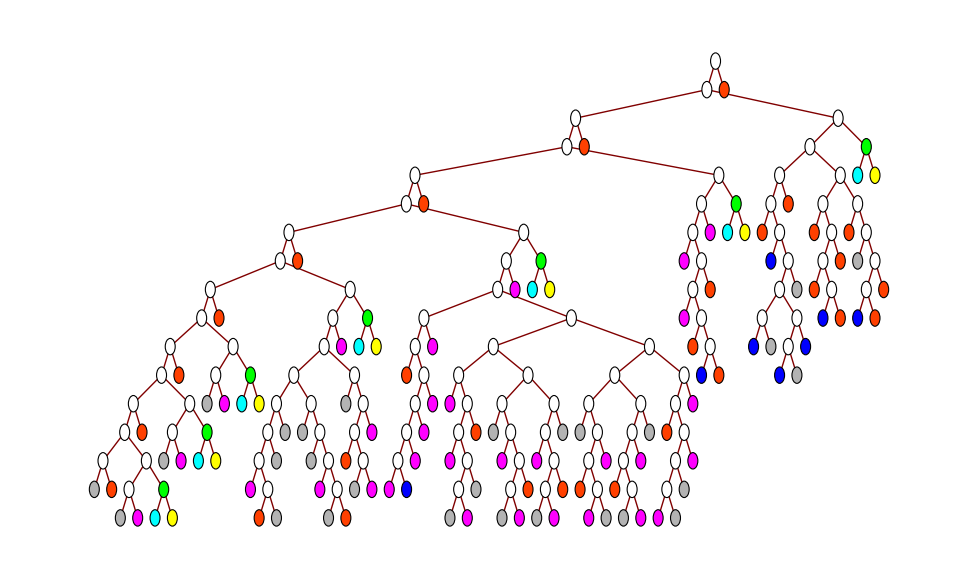

```mathematica
myTree=treeGen[1,3,seqData,20];
TreePlot[myTree,Top,myTree[[1,1]],
VertexRenderingFunction->(Tooltip[{vertexColor[#2[[4]]],EdgeForm[Black],Disk[#,.15]},ToString[#2[[1]]]<>"("<>ToString[#2[[2]]]<>")\n"<>listToString[#2[[3]],#2[[4]],#2[[5]]]]&)]
```

We can look at particular sub-trees in the following way:

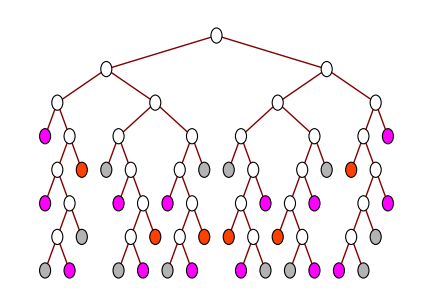

```mathematica
myTree=treeGen[2305,12,seqData,20];
TreePlot[myTree,Top,myTree[[1,1]],
VertexRenderingFunction->(Tooltip[{vertexColor[#2[[4]]],EdgeForm[Black],Disk[#,.15]},ToString[#2[[1]]]<>"("<>ToString[#2[[2]]]<>")\n"<>listToString[#2[[3]],#2[[4]],#2[[5]]]]&)]
```

The following diagram appears in the article. It displays the value of d on each vertex.

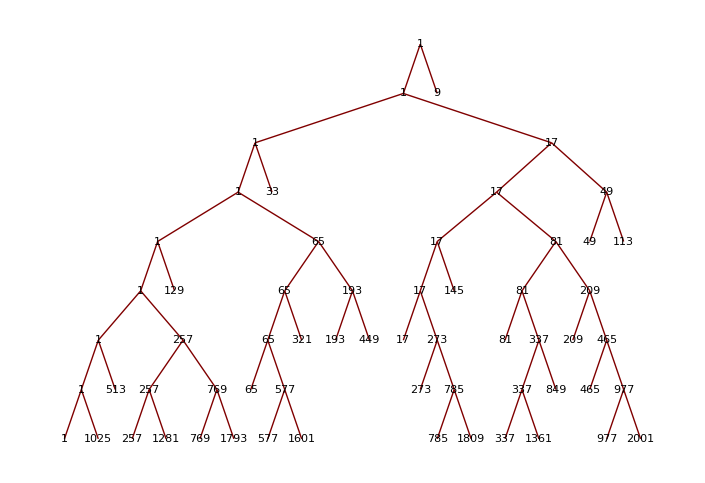

```mathematica
myTree=treeGen[1,3,seqData,11];
TreePlot[myTree,Top,myTree[[1,1]],VertexLabeling->True,
VertexRenderingFunction->(Text[Framed[ToString[#2[[1]]],Background->vertexColor[#2[[4]]]],#1]&)]
```

### Sequence Exploration

getSeq grabs the fnAbs for d (m) from seqData and displays it nicely using listToString. This is a useful when looking at very long fnAbs.

```mathematica
getSeq[d_,m_,seqData_]:=Module[{entry},
	entry = Select[seqData,#[[1;;2]]=={d,m}&][[1]];
	Return[listToString[entry[[3]],entry[[4]],entry[[5]]]];
];
```

```mathematica
getSeq[2001,11,seqData]
```

22121221212224